# Two elastic disks, a and b, bouncing in a square : a variant of the gas of Szilard.

## The initial conditions are clearly apparent from the following figure (Arbitrary units) :

```mathematica
m=2;L=1;R=2/10;xa[0]=0.2;ya[0]=0.2;xb[0]=0.6;yb[0]=0.7;vxa[0]=2.;vya[0]=1.;vxb[0]=-1.;vyb[0]=1.;t[0]=0;
```

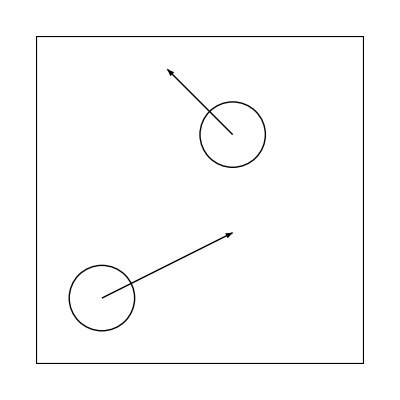

```mathematica
Graphics[{FaceForm[White],EdgeForm[Directive[Thick]],Rectangle[],Thick,Circle[{xa[t[0]],ya[t[0]]},R],Circle[{xb[t[0]],yb[t[0]]},R],Arrow[{{xa[t[0]],ya[t[0]]},{xa[t[0]],ya[t[0]]}+2/10{vxa[t[0]],vya[t[0]]}}],Arrow[{{xb[t[0]],yb[t[0]]},{xb[t[0]],yb[t[0]]}+2/10{vxb[t[0]],vyb[t[0]]}}]}]
```

## Time evolution : each collision (one wall or the other disk) is named an “event” (9 possibilities). Events are labeled by integer j. Multiple collisions are forbidden (The program halts prematurely). Cible[j] is an integer (∈{1,...,9}) memorizing the type of event.

```mathematica
Do[{events[j]=Flatten[{time/.Solve[{xa[j-1]+vxa[j-1](time-t[j-1])==L-R,R≤ya[j-1]+vya[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{ya[j-1]+vya[j-1](time-t[j-1])==L-R,R≤xa[j-1]+vxa[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{xa[j-1]+vxa[j-1](time-t[j-1])==R,R≤ya[j-1]+vya[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{ya[j-1]+vya[j-1](time-t[j-1])==R,R≤xa[j-1]+vxa[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{xb[j-1]+vxb[j-1](time-t[j-1])==L-R,R≤yb[j-1]+vyb[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{yb[j-1]+vyb[j-1](time-t[j-1])==L-R,R≤xb[j-1]+vxb[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{xb[j-1]+vxb[j-1](time-t[j-1])==R,R≤yb[j-1]+vyb[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{yb[j-1]+vyb[j-1](time-t[j-1])==R,R≤xb[j-1]+vxb[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time],time/.Solve[{(xa[j-1]+vxa[j-1](time-t[j-1])-xb[j-1]-vxb[j-1](time-t[j-1]))^2+(ya[j-1]+vya[j-1](time-t[j-1])-yb[j-1]-vyb[j-1](time-t[j-1]))^2==4 R^2,R≤xa[j-1]+vxa[j-1](time-t[j-1])≤L-R,R≤ya[j-1]+vya[j-1](time-t[j-1])≤L-R,R≤xb[j-1]+vxb[j-1](time-t[j-1])≤L-R,R≤yb[j-1]+vyb[j-1](time-t[j-1])≤L-R,time>t[j-1]+10^-10},time,Reals]}],
t[j]=Min[Cases[events[j],u_/;u>t[j-1]]],
multiplicity[j]=Count[events[j],t[j]] ,If[multiplicity[j]>1,{Print[j," Multiple collisions"],Abort}],
cible[j]=Position[events[j],t[j]][[1,1]],
xa[j]=xa[j-1]+vxa[j-1](t[j]-t[j-1]),ya[j]=ya[j-1]+vya[j-1](t[j]-t[j-1]),xb[j]=xb[j-1]+vxb[j-1](t[j]-t[j-1]),yb[j]=yb[j-1]+vyb[j-1](t[j]-t[j-1]),vxa[j]=vxa[j-1];vya[j]=vya[j-1],vxb[j]=vxb[j-1];vyb[j]=vyb[j-1],Switch[cible[j],1,vxa[j]=-vxa[j-1],2,vya[j]=-vya[j-1],3,vxa[j]=-vxa[j-1],4,vya[j]=-vya[j-1],5,vxb[j]=-vxb[j-1],6,vyb[j]=-vyb[j-1],7,vxb[j]=-vxb[j-1],8,vyb[j]=-vyb[j-1],9,{{vxa[j],vya[j]}={vxa[j-1],vya[j-1]}-1/(4 R^2){xa[j]-xb[j],ya[j]-yb[j]} {xa[j]-xb[j],ya[j]-yb[j]}.{vxa[j-1]-vxb[j-1],vya[j-1]-vyb[j-1]},{vxb[j],vyb[j]}={vxb[j-1],vyb[j-1]}+1/(4 R^2){xa[j]-xb[j],ya[j]-yb[j]} {xa[j]-xb[j],ya[j]-yb[j]}.{vxa[j-1]-vxb[j-1],vya[j-1]-vyb[j-1]}}] },{j,50000}]
```

## Checking the conservation of energy :

```mathematica
Table[vxa[j]^2+vya[j]^2+vxb[j]^2+vyb[j]^2,{j,0,50000,1000}]
```

{7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.}

## 50000 events have been calculated, 36 are displayed here :

```mathematica
GraphicsGrid[Partition[Table[Graphics[{FaceForm[White],EdgeForm[Directive[Thick]],Rectangle[],Thick,Circle[{xa[j],ya[j]},R],Circle[{xb[j],yb[j]},R],Arrow[{{xa[j],ya[j]},{xa[j],ya[j]}+2/10{vxa[j],vya[j]}}],Arrow[{{xb[j],yb[j]},{xb[j],yb[j]}+2/10{vxb[j],vyb[j]}}]}],{j,0,35}],6]]
```

-Graphics-

## Histogram of the kinetic energy ratio, K_a/K_b : the maximum corresponds to the equipartition.

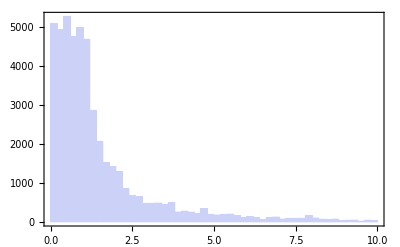

```mathematica
Histogram[Table[(vxa[j]^2+vya[j]^2)/(vxb[j]^2+vyb[j]^2),{j,1,50000}],{0,10,0.2},Frame->True,FrameLabel->{"K(a)/K(b)"},LabelStyle->Directive[Medium,Bold]]
```

## Mean time between two collisions (a and b) :

```mathematica
Table[cible[j],{j,20}]         (*In the table of events, figures "9" predict a collision between a and b*)
```

{6,9,6,1,7,4,3,9,4,5,6,1,7,9,7,1,6,4,9,4}

```mathematica
Count[Table[cible[j],{j,50000}],9]      (*Number of collisions between a and b after 500000 events*)
```

25751

```mathematica
Thread[t[Flatten[Position[Table[cible[j],{j,20}],9]]]]      (*4 first collision times*)
```

{0.151962,0.581427,1.08068,1.37242}

```mathematica
Differences[Thread[t[Flatten[Position[Table[cible[j],{j,20}],9]]]]]       (*Times elapsed between them*)
```

{0.429465,0.499249,0.291747}

```mathematica
Mean[Differences[Thread[t[Flatten[Position[Table[cible[j],{j,50000}],9]]]]]]        (*Mean time averaged on 25751 collisions*)
```

0.116231

```mathematica
t[50000]
```

2993.1

```mathematica
2993.1/25751.      (*Simpler indeed !*)
```

0.116232

```mathematica
timescoll=Flatten[Position[Table[cible[j],{j,50000}],9]];     (*Times of successive collisions between a and b*)
```

```mathematica
(Table[(vxa[timescoll[[j]]]^2+vya[timescoll[[j]]]^2),{j,25750}].Differences[Thread[t[Flatten[Position[Table[cible[j],{j,50000}],9]]]]])/Total[Differences[Thread[t[Flatten[Position[Table[cible[j],{j,50000}],9]]]]]]    (*Mean kinetic energy of a*)
```

3.48737

```mathematica
(Table[(vxb[timescoll[[j]]]^2+vyb[timescoll[[j]]]^2),{j,25750}].Differences[Thread[t[Flatten[Position[Table[cible[j],{j,50000}],9]]]]])/Total[Differences[Thread[t[Flatten[Position[Table[cible[j],{j,50000}],9]]]]]]        (*Mean kinetic energy of b*)
```

3.51263